```mathematica
(* Re-creation of Zhabotinsky 2000 (Biophys J) *)
```

```mathematica
(* Parameter Declarations *)
concCa = 0.1; (* Sweep bet/ 0.1 and 1 *)
ek = 20; (* Initial concentration of CaMKII *)
ep0 = 0.1;   (* Initial concentration of phosphatase *)
I0 = 0.1; (* Initial concentration of free Inhibitor 1 *)
KM = 0.4; (*Michaelis constant of phosphatase *)
Kh2 = 0.7; (*Ca2+ activation Hill constant of CaN *)

(*These parameters are held constant in all simulations *)
Kh1 = 4; (*Ca2+ activation Hill constant of CaMKII *)
Vcan = 1; (* Activity of CaN divided by its Michaelis constant *)
Vpka = 1; (*Activity of PKA divided by its Michaelis constant *)
k1 = 0.5 ;(*Catalytic constant of autophos. *)
k2 = 2; (*Catalytic constant of phosphatase *)
k3 = 1; (* association rate constant of PP1-I1p complex *)
k4 = 0.0011; (* dissociation rate constant of the PP1-I1p complex *)
```

```mathematica
InitialConditions ={
Ca[0]== concCa,

P0[0] == ek,
P1[0] == 0,
P2[0] ==0,
P3[0] ==0,
P4[0] == 0,
P5[0]==0,
P6[0]==0,
P7[0]==0,
P8[0]==0,
P9[0]==0,
P10[0]==0,

ep[0] == ep0,
Inh[0] == I0,

v1[0]==0,
v2[0]==0,
v3[0]==0
};
```

```mathematica
Eqns = 
{{
(*Future: approximate the cam-dependent PP exclusion by dividing the v3 terms by a factor determined empirically from the MCell dodecamer model *)
P0'[t] == -v1[t] + v3 [t]*P1[t],
P1'[t] == v1[t] - v3 [t]*P1[t] -v2[t]* P1[t] +2v3[t]* P2[t],
P2'[t] == v2 [t]*P1[t] -2v3[t]* P2[t] - 1.8v2 [t]*P2[t] + 3v3[t]* P3[t],
P3'[t] == 1.8v2[t]* P2[t] - 3v3[t]* P3[t]-2.3v2[t]* P3[t]+4v3[t]* P4[t],
P4'[t] == 2.3v2[t]* P3[t] -4v3[t]* P4[t] -2.7v2[t]* P4[t] + 5v3[t]* P5[t],
P5'[t] == 2.7v2[t]* P4[t] -5v3[t]* P5[t] -2.8v2[t]* P5[t] + 6v3 [t]*P6[t],
P6'[t] == 2.8v2[t]* P5[t] - 6v3[t]* P6[t] -2.7v2[t]* P6[t] +7v3[t]* P7[t],
P7'[t] == 2.7v2 [t]*P6[t] -7v3[t]* P7[t] - 2.3v2[t]* P7[t] +8v3[t]* P8[t],
P8'[t] == 2.3v2 [t]*P7[t] -8v3 [t]*P8[t] -1.8v2 [t]*P8[t] + 9v3[t]* P9[t],
P9'[t] == 1.8v2[t]* P8[t] -9v3[t]* P9[t] -v2 [t]*P9[t] + 10v3[t]* P10[t],
P10'[t] == v2[t]* P9[t] - 10v3[t]* P10[t],
ep'[t] == -k3 Inh[t] ep[t] + k4*(ep0 -ep[t]),
Inh'[t] == -k3 Inh[t] ep[t] + k4*(ep0 -ep[t]) + Vpka I0 - (Vcan Inh[t]*(Ca[t]/Kh2)^3)/(1+(Ca[t]/Kh2)^3)
},
{P0,P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,ep,Inh}};
```

```mathematica
ODEs=Eqns[[1]];
Vars=Eqns[[2]];
AppendTo[ODEs,InitialConditions];

fList = {100};
f= fList[[1]];
sig=.0025; (* Sigmoid half width (sec) *)
Act=1; (*time when activation occurs*)
Ca0 = concCa;
tau = 0.02; (*Time constant from Zhabotinsky 2000 *)
numpulse = 100; (*number of Ca2+ pulses *) 
peak = 12;

Clear[g,G,Ca];
g=Table[,numpulse];
For[pulse =0,pulse<numpulse,pulse++, (* Limit to 100 Pulses regardless of freq *)
s =  0.5*(1/f)+pulse*(1/f);
g[[pulse+1]]=(peak-Ca0)*Exp[-(((t-Act)-s)^2/(2*sig^2))];
];
g = Flatten[g];
G[t] = Ca0;
For[k=1,k≤pulse,k++,G[t]=G[t]+g[[k]]];

Ca[t] = G[t];

(*Ca[t] =  Ca0 + peak*Sum[Exp[-i/(f*tau)],{i,numpulse}];*) (*Is this time dependent? *)  

v1[t] = (10k1 P0[t]*(Ca[t]/Kh1)^8)/((1+ (Ca[t]/Kh1)^4)^2);
v2[t] = (k1 P1[t]*(Ca[t]/Kh1)^4)/(1+(Ca[t]/Kh1)^4);
v3[t] = (k2 ep[t])/(KM + P1[t] +2P2[t] +3P3[t] + 4P4[t] + 5P5[t]+6P6[t]+7P7[t] +8P8[t] +9P9[t]+10P10[t]);

EqnSys = Flatten[ODEs];
Soln=NDSolve[EqnSys,Vars,{t,0,2*(Act+numpulse/f)},AccuracyGoal-> 10, PrecisionGoal -> 10,MaxStepSize->sig/2];
```

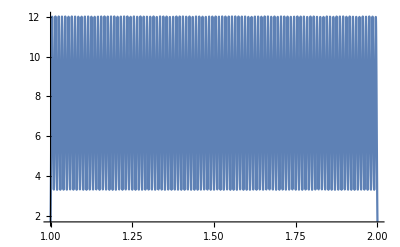

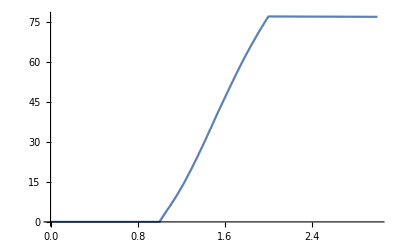

```mathematica
outputVar = {P1[t]+2P2[t]+3P3[t]+4P4[t]+5P5[t]+6P6[t]+7P7[t]+8P8[t]+9P9[t]+10P10[t]}; 
Plot[Evaluate[Ca[t] /. Soln],{t,1,2}, PlotRange-> All]
Plot[Evaluate[outputVar/.Soln],{t,0,3}, PlotRange-> All]
```

```mathematica
Flatten[Evaluate[outputVar/. Soln /. t-> 3]]
```

{76.8364}